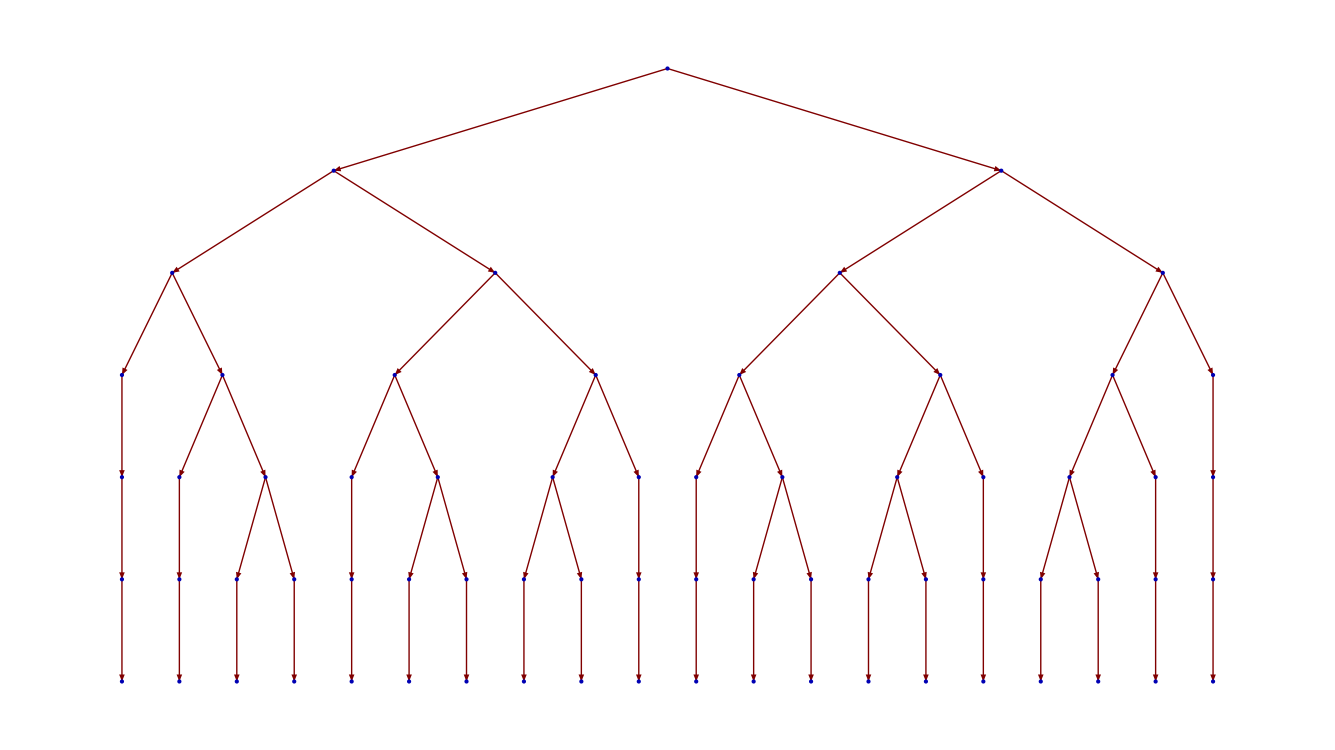

20

```mathematica
(*state is {x,r}*)
ReadFunc[state_]:=(x1=state[[1]];r1=state[[1]];Return[{x1,r1}])
IncFunc[state_]:=(x1=state[[1]];r1=state[[2]]+1;Return[{x1,r1}])
WriteFunc[state_]:=(x1=state[[2]];r1=state[[2]];Return[{x1,r1}])
program={ReadFunc,IncFunc,WriteFunc};
programNames={"read(x,R)","inc(R)","write(R,x)"};
GetProgramName[procIdx_,counter_]:=ToString[procIdx]<>":"<>programNames[[counter]];

tree={};
endStates=0;
FillTree[step_,counter0_,counter1_,state_]:=(
If[counter0<4,
state1=program[[counter0]][state];
programName=GetProgramName[1,counter0];
AppendTo[tree,{{state,step}->{state1,step<>"\n"<>programName},programName}];
FillTree[step<>"\n"<>programName,counter0+1,counter1,state1];
];
If[counter1<4,
state2=program[[counter1]][state];
programName=GetProgramName[2,counter1];
AppendTo[tree,{{state,step}->{state2,step<>"\n"<>programName},programName}];
FillTree[step<>"\n"<>programName,counter0,counter1+1,state2];
];
If[counter0==4&&counter1==4,endStates++];
);
initialState={0,"?"};
FillTree["",1,1,initialState]
TreePlot[tree,DirectedEdges->True]
endStates
```

```mathematica
tree={};
endStates=0;
FillTree[step_,counter0_,counter1_,counter2_,state_]:=(
If[counter0<4,
state1=program[[counter0]][state];
programName=GetProgramName[1,counter0];
AppendTo[tree,{{state,step}->{state1,step<>"\n"<>programName},programName}];
FillTree[step<>"\n"<>programName,counter0+1,counter1,counter2,state1];
];
If[counter1<4,
state2=program[[counter1]][state];
programName=GetProgramName[2,counter1];
AppendTo[tree,{{state,step}->{state2,step<>"\n"<>programName},programName}];
FillTree[step<>"\n"<>programName,counter0,counter1+1,counter2,state2];
];
If[counter2<4,
state3=program[[counter2]][state];
programName=GetProgramName[3,counter2];
AppendTo[tree,{{state,step}->{state3,step<>"\n"<>programName},programName}];
FillTree[step<>"\n"<>programName,counter0,counter1,counter2+1,state3];
];
If[counter0==4&&counter1==4&&counter2==4,endStates++];
);
initialState={0,"?"};
FillTree["",1,1,1,initialState]
Export["plot.jpg",TreePlot[tree,ImageSize->8192]]
endStates
```

plot.jpg

1680